#Quit[]

{Rxrx'[t] m/s,Rxry'[t] m/s,Rxrz'[t] m/s}

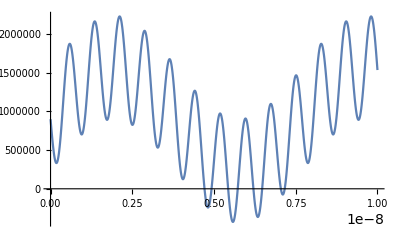

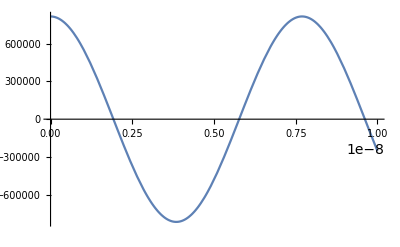

```mathematica
#Quit[]
(* Weber force between charges in motion to see what the plasma Rx antenna would feel in the null of the Tx due to charges in motion in each.

The scope trace is at the bottom and resembles the dot product "fringe physics" term often associated with "lonitudinal waves" or "scalar waves" people often palaver about but rarely have a rigorous model for.  In the case of our experiments, the scope traces we sare are reflected in the blow simulated tradces in every respect including the phase relationships.

The charge drift velocity in the Tx is assumed to be small by comparison with the Rx charge drift velocity.Weber's force is not relativistically corrected.Phipps has a version that is relativistically corrected so that's next on my agenda and is necessary since we expect the NE2 bulb plasma electrons to be going c/10 according to Natalia Nikolova's Matlab model she used for her patent with Robert Zimmerman.
https://patents.google.com/patent/US8165531B2/

Chalmers Sherwin found Phipps's version did not fit radar behavior.
https://citeseerx.ist.psu.edu/document?repid=rep1&type=pdf&doi=b321457980f724d2dbe2de9ee4700f616a6377b7

This doesn't surprise me in the least and I'm rather surprised neither he nor Phipps thought to investigate what I did when I was driven to consider Phipps's  model:

Any version of Weber electrodynamics must try to model the wave equation and will likely have to resort to something like the Dirac Sea of Charge Pairs so as to incorporate Weber's original derivation of the speed of light for telegraphy.

Indeed a 2023 paper did precisely that derivation.
https://www.mdpi.com/2673-9321/3/2/24

*)
(*SetDirectory[NotebookDirectory[]]
Get["CODATAstuff.wl"]*)
ClearAll["Global`*"]
QuantityVector[name_String,components_List,unit_,vars_List:{}]:=Module[{syms},If[Length[vars]>0,syms=Quantity[Symbol[name<>#][Sequence@@vars],unit]&/@components,syms=Quantity[Symbol[name<>#],unit]&/@components];
syms]
Q=Quantity[QM,"Coulombs"];
q=Quantity[qM,"Coulombs"];
(*Txhertz=Quantity[TxhertzM,"Seconds^-1"];
Rxhertz=Quantity[RxhertzM,"Seconds^-1"];*)
(*tQuantity = Quantity[t,"Seconds"];*)
subs1= {
Txrx->Function[0],
Txry->Function[0],
Txrz->Function[100+TxAntennaLengthM*Sin[# 2 Pi Txhertz] ],
Rxrx->Function[0],
Rxry->Function[0],
Rxrz->Function[RxAntennaLengthM Sin[# 2 Pi Rxhertz]]};
subs2={Txhertz->1.3*10^9,Rxhertz->1.3*10^8,qM->1,QM->1,TxAntennaLengthM->.00001,RxAntennaLengthM->.001};
subs3={t->1/10^9};
(*rVec=QuantityVector["r",{"x","y","z"},"Meters"]*)
(* Transmitter and Receiver (Tx Rx) relative position as a function of time *)
Txr=QuantityVector["Txr",{"x","y","z"},"Meters",{t}];
Rxr=QuantityVector["Rxr",{"x","y","z"},"Meters",{t}];
vRx = D[Rxr,Quantity[t,"Seconds"]] (* velocity of the receiving antenna's charge *)
rVec=Txr-Rxr;
vVec=D[rVec,Quantity[t,"Seconds"]];
aVec=D[vVec,Quantity[t,"Seconds"]];
c=Quantity["SpeedOfLight"];(*Speed of light in m/s*)
epsilon0=Quantity["ElectricConstant"];
rUnitVec=rVec/Norm[rVec];
DVecs=(vVec.vVec-3/2 ((rUnitVec).vVec)^2+Norm[rVec] rUnitVec.aVec); (* m^2/s^2 *)
DVecsDimensionless = (1+ DVecs/c^2);
weberForce[t_]=(Q q rUnitVec)/(4 Pi epsilon0 Norm[rVec]^2)*DVecsDimensionless;

(* Note carefully that *xhertz is previously defined in terms of *xhertM.  Therefore *xhertzM is what is being substituted. *)
plotWeber[t_]=UnitConvert[weberForce[t]/.subs1/.subs2];
Plot[plotWeber[t][[3]],{t,0,1/10^8}]
Plot[vRx[[3]]/.subs1/.subs2,{t,0,1/10^8}]
```